# DN2

## 1.1 Računanje vrednosti števila π - Monte Carlo

```mathematica
(*Tu pokličem datotečno funkcijo, ki sem jo definiral v datoteki s končnico .m, katera vrne koordinate točk, ki ležijo znotraj kvadrata in koordinate točk, ki ležijo znotraj kroga.
OBVEZNO SPREMENI POT, KJER JE SHRANJENA DATOTEKA mccpi.m!*)
Get["I:\\FAKS\\3.LETNIK\\5. semester\\Napredna računalniška orodja\\DN\\DN2\\mccpi.m"]
```

```mathematica
(*Definiram glavno funkcijo, katera izračuna približno vrednost π, ter njeno napako*)
calcpi[st_]:=Module[{pipribl,napaka},
(*Prikažem okno, v katerega vpišem število točk, ki jih želim uporabiti za izračun*)
sttock=Input["Naključno število točk:"];

(*Shranim koordinate s funkcijo mccpi*)
{ktkvad,ktkrog}=mccpi[sttock];
(*Preštejem točke, ki ležijo znotraj kroga*)
stkrog=Count[Norm/@ktkvad,_?(#<1&)];

(*Izračunam približno vrednost π, ter njeno napako*)
pipribl=N[4 stkrog/sttock];
napaka=pipribl-Pi;

(*Izpišem*)
Print["Pribljižna vrednost π: ",pipribl ];
Print["Napaka π: ",napaka ];

(*Vse prikažem na enem grafu s funkcijo Show*)
p1=ListPlot[ktkvad,PlotLegends->{"Točke zunaj kroga"},PlotStyle->Thick];
p2=ListPlot[ktkrog,PlotLegends->{"Točke znotraj kroga"},PlotStyle->Red,PlotStyle->Thick];
p3=ParametricPlot[{Sin[fi],Cos[fi]},{fi,0,2Pi},PlotStyle->Black];
Show[p1,p2,p3,PlotLabel->"Monte Carlo",AspectRatio->1,AxesLabel->{"x-koordinate","y-koordinate"},PlotRange->{{-1,1},{-1,1}}]
]
```

Pribljižna vrednost π: 3.08

Napaka π: -0.0615927

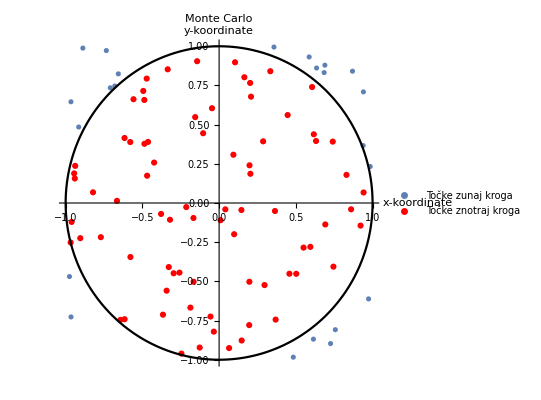

```mathematica
(*Funkcijo calcpi pokličem, za število točk, ki jih vpišem v vhodno okno.
Funkija izpiše vrednosti in izriše graf*)
calcpi[sttock]
```

## 1.2 Razvoj v vrsto in funkcija Manipulate

```mathematica
(*S funkcijo manipulate upravljamo red aproksimacijskih Taylorjevih vrst, s katerimi aproksimiram funkcijo f[t]. Na grafu izrišem pravo funkcijo ter njeno aproksimacijo, kjer spreminjam red Taylorjeve vrste.*)

Manipulate[Module[{f, f1},
(*Funkcija f[t]*)
f[t_] := Sin[t] * t^2 * Exp[-t];
(*Approksimacija funkcije f[t]-Taylorjeva vrsta razvita okoli točke t->2*)
f1 = Normal[Series[f[t], {t, 2, n}]];
(*Graf obeh funkcij*)
Plot[{f[t], f1}, {t, 0, 4}, PlotRange -> All, PlotLegends ->{"f[t]", Row[{"Taylorjeva aproksimacija reda: ", n}]}]],
{{n, 3, "Red aproksimirane Taylorjeve vrste: "}, 1, 10, 1}
]
```

Kar lahko opazimo  je, da se z višanjem reda vse bolj približujemo pravi funkciji f[t]!